```mathematica
segment = {{0 , 1},{2 , 5}};
```

```mathematica
(segment[[2]] - segment[[1]])/(√((segment[[2]] - segment[[1]]).(segment[[2]] - segment[[1]])))
```

{1/(√5),2/(√5)}

```mathematica
segr = Normalize[segment[[2]] - segment[[1]]]
```

{1/(√5),2/(√5)}

```mathematica
?Cross
```

```mathematica
segr
```

{1/(√5),2/(√5)}

```mathematica
norm = Join[segr , {0}]×{0 , 0 , 1}
```

{2/(√5),-1/(√5),0}

```mathematica
norm = Join[segr , {0}]×{0 , 0 , -1}
```

{-2/(√5),1/(√5),0}

```mathematica
norm.norm
```

1

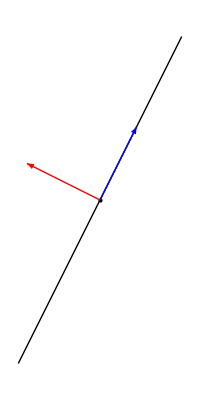

```mathematica
Graphics[{Line[segment] , {PointSize[Large],Point[0.5 (segment[[1]] + segment[[2]])]},{Blue , Arrowheads[0.1],Arrow[{0.5 (segment[[1]] + segment[[2]]) , 0.5 (segment[[1]] + segment[[2]]) + segr}]} , {Red,Arrowheads[0.1],Arrow[{0.5 (segment[[1]] + segment[[2]]) , 0.5 (segment[[1]] + segment[[2]]) + norm[[1;;2]]}]}}]
```

```mathematica
RotationMatrix[π/2]//MatrixForm
```

(0 | -1
1 | 0)

```mathematica
RotationMatrix[-π/2]//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
triangle = {{0 , 0 , 1} , {0 , 1 , 0} , {1 , 0 , 1}};
```

```mathematica
r1 = Normalize[triangle[[2]] - triangle[[1]]]
```

{0,1/(√2),-1/(√2)}

```mathematica
r2 = Normalize[triangle[[3]] - triangle[[1]]]
```

{1,0,0}

```mathematica
r1.r1
```

1

```mathematica
r2.r2
```

1

```mathematica
norm1 = r1×r2
```

{0,-1/(√2),-1/(√2)}

```mathematica
norm1.norm1
```

1

```mathematica
norm2 = r2×r1
```

{0,1/(√2),1/(√2)}

```mathematica
norm2.norm2
```

1

```mathematica
Graphics3D[{Polygon[triangle] , {Blue , Arrow[{triangle[[1]] , triangle[[1]] + r1}] , Arrow[{triangle[[1]] , triangle[[1]] + r2}]},{Red , Arrow[{triangle[[1]] , triangle[[1]] + norm1}]}}]
```

-Graphics3D-